Шаг h

0.375

a)

(0.5
0.875
1.25
1.625
2.) (4.
1.30612
0.64
0.378698
0.25)

б)

4.00000 | -7.18367 |  7.20980 | -5.12927 |  2.84596
 1.30612 | -1.77633 |  1.43936 | -0.86034 | 
 0.64000 | -0.69680 |  0.47148 |  | 
 0.37870 | -0.34320 |  |  | 
 0.25000 |  |  |  |

в)

ColumnForm[lst:]

4.-7.18367 (-0.5+x)
4.-7.18367 (-0.5+x)+7.2098 (-0.875+x) (-0.5+x)
4.-7.18367 (-0.5+x)+7.2098 (-0.875+x) (-0.5+x)-5.12927 (-1.25+x) (-0.875+x) (-0.5+x)
4.-7.18367 (-0.5+x)+7.2098 (-0.875+x) (-0.5+x)-5.12927 (-1.25+x) (-0.875+x) (-0.5+x)+2.84596 (-1.625+x) (-1.25+x) (-0.875+x) (-0.5+x)

ColumnForm[Collect[lst,x]]:

7.59184-7.18367 x
10.7461-17.0971 x+7.2098 x^2
13.5512-28.1571 x+20.6741 x^2-5.12927 x^3
16.0803-39.6855 x+38.9505 x^2-17.2246 x^3+2.84596 x^4

г)

16.0804-39.6857 x+38.9507 x^2-17.2247 x^3+2.84598 x^4

д)

[0.125, 2.375]

-Graphics-

[-0.25, 2.75]

-Graphics-

e)

2.84596
-5.12927+2.84596 (-1.625+x)
7.2098+(-5.12927+2.84596 (-1.625+x)) (-1.25+x)
-7.18367+(7.2098+(-5.12927+2.84596 (-1.625+x)) (-1.25+x)) (-0.875+x)
4.+(-7.18367+(7.2098+(-5.12927+2.84596 (-1.625+x)) (-1.25+x)) (-0.875+x)) (-0.5+x)

(0.5
0.5375
0.575
0.6125
0.65
0.6875
0.725
0.7625
0.8
0.8375
0.875
0.9125
0.95
0.9875
1.025
1.0625
1.1
1.1375
1.175
1.2125
1.25
1.2875
1.325
1.3625
1.4
1.4375
1.475
1.5125
1.55
1.5875
1.625
1.6625
1.7
1.7375
1.775
1.8125
1.85
1.8875
1.925
1.9625
2.) (4.
3.46133
3.02457
2.66556
2.36686
2.1157
1.9025
1.71997
1.5625
1.42571
1.30612
1.20098
1.10803
1.02548
0.951814
0.885813
0.826446
0.772854
0.72431
0.6802
0.64
0.603261
0.569598
0.538675
0.510204
0.483932
0.459638
0.437129
0.416233
0.396801
0.378698
0.361807
0.346021
0.331246
0.317397
0.3044
0.292184
0.280689
0.26986
0.259645
0.25) (4.
3.5652
3.17572
2.82811
2.51906
2.2454
2.00407
1.79219
1.60697
1.44578
1.30612
1.18563
1.08206
0.993334
0.917483
0.852683
0.797242
0.749607
0.708355
0.672203
0.64
0.610731
0.583515
0.557609
0.532401
0.507418
0.482318
0.456899
0.43109
0.404956
0.378698
0.352652
0.327289
0.303213
0.281167
0.262025
0.246799
0.236635
0.232814
0.236752
0.25)

(0.
0.10387
0.151144
0.162554
0.152197
0.129694
0.101577
0.072222
0.044471
0.0200749
2.22045×10^-16
0.0153499
0.0259715
0.0321422
0.0343311
0.0331305
0.029204
0.023247
0.0159544
0.00799667
3.33067×10^-16
0.00746934
0.0139175
0.0189335
0.022197
0.0234856
0.0226804
0.0197704
0.0148566
0.00815511
6.10623×10^-16
0.00915454
0.0187321
0.0280327
0.0362308
0.0423747
0.0453852
0.0440546
0.0370463
0.0228938
1.33227×10^-15)

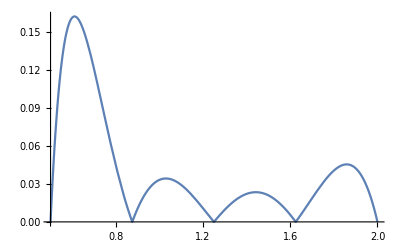

{0.162599,{2.→0.610099}}

```mathematica
a = 0.5;b=2;n =4;
"Шаг h" 
 h = (b-a)/n
"a)"
XDT = {}; YDT ={};
For[i=0,i<=n,i++,
xdata[i] = a+i×h;
ydata[i]=N[1/(xdata[i])^2];
XDT = Append[XDT,xdata[i]];
YDT= Append[YDT, ydata[i]];
];
Array[xdata,{n+1,0}];
Array[ydata,{n+1,0}];
MatrixForm[XDT]   MatrixForm[YDT]
"б)"
Array[difftab,{n+1, n+1}, {0,0}];
For[i=1,i<=n,i++,
For[j=n,j>=n-i,j--,difftab[j,i]= ""]];
For[j=0,j<=n,j++,difftab[j,0]=ydata[j]];
For[i=1,i<=n,i++,
For[j=0,j<=n-i,j++,
difftab[j,i]=(difftab[j+1,i-1]-difftab[j,i-1])/(xdata[i+j]-xdata[j])]];
arr = Array[difftab,{n+1,n+1},{0,0}];
PaddedForm[TableForm[arr],{6,5}]
"в)"
pln = difftab[0,0]+difftab[0,1]*(x-xdata[0]);
lst = List[pln];
For[i=2,i<=n,i++,
pln=lst[[i-1]]+difftab[0,i]*∏_(i=0)^(i-1) (x-xdata[i]);
lst=Append[lst,pln]];
nwtn[x_]:=N[lst[[n]]];
"ColumnForm[lst:]"
ColumnForm[lst]
"ColumnForm[Collect[lst,x]]:"
ColumnForm[Collect[lst,x]]
"г)"
data = {{0.5,4.0},{0.875,1.30612},{1.25,0.64},{1.625,0.378698},{2.0,0.25}};
inpln:=InterpolatingPolynomial[data,x];
Collect[inpln,x]
"д)"
"[0.125, 2.375]"
Plot[{1/x^2,nwtn[x_]},{x,0.125,2.375},PlotLabels->"Expressions"]
"[-0.25, 2.75]"
Plot[{1/x^2,nwtn[x_]},{x,-0.25,2.75},PlotLabels->"Expressions"]
"e)"
Pln={};P[n+1]=0;
For[i=n,i>=0,i--,
P[i]=difftab[0,i]+(x-xdata[i])*P[i+1];
Pln=Append[Pln,P[i]];]
ColumnForm[Pln] 

nwtn[x_]:=P[0];
m=40;
XDAT ={};YDAT ={};
nwtnDAT={}; MR={};
For[i=0,i<=m,i++,
xdat[i]=a+i×h/10;
ydat[i]=N[1/(xdat[i])^2];
x=xdat[i];
nwtndat[i]=nwtn[x];
mr[i]= Abs[ydat[i]-nwtndat[i]];
XDAT=Append[XDAT,xdat[i]];
YDAT=Append[YDAT,ydat[i]];
nwtnDAT=Append[nwtnDAT,nwtndat[i]];
MR=Append[MR,mr[i]];];

MatrixForm[N[XDAT]]  MatrixForm[YDAT]  MatrixForm[nwtnDAT]
MatrixForm[MR]
Plot[Abs[1/(x*x)-nwtn[x]],{x,0.5,2}]
FindMaximum[{Abs[1/(x*x)-nwtn[x]],0.5<=x<=2},{x,0.6}]
```